Various calculations for MOT beam clearance in the network experiment.

Clearance between 0.4 NA JenOptik lens and a free-space MOT beam in the network experiment.

See page 217 of my turquoise Leuchtturm journal.

minimum angle

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1→34.9539}}

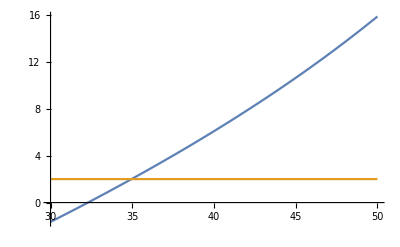

```mathematica
(*units in mm*)
d1 = 10;(*MOT to glass*)
t = 7.36;(*fused silica thickness*)
d3 = 1.2;(*glass to lens*)
w0=0.5;(*beam waist*)
clearance=2;
ϕlens=19.97;(*lens diameter by glass*)
n2=1.4537; (*fused silica IOR @780*)
"minimum angle"
NSolve[(d1 Tan[θ1 π/180 ]+t Tan[ArcSin[Sin[θ1 π/180]/n2]]+d3 Tan[θ1 π/180]-ϕlens/2)/w0==clearance,θ1]
Plot[{(d1 Tan[θ1 π/180 ]+t Tan[ArcSin[Sin[θ1 π/180]/n2]]+d3 Tan[θ1 π/180]-ϕlens/2)/w0,clearance},{θ1,30,50}]
```

Radius at which beam comes out of the glass window by the lens:

```mathematica
(d1 Tan[θ1 π/180 ]+t Tan[ArcSin[Sin[θ1 π/180]/n2]])/.θ1->35
```

10.1625

Radius at which beam intersects the glass window inside the chamber:

```mathematica
(d1 Tan[θ1 π/180 ])/.θ1->35
```

7.00208

```mathematica
(d1 Tan[θ1 π/180 ]+t Tan[ArcSin[Sin[θ1 π/180]/n2]]+d3 Tan[θ1 π/180]-ϕlens/2)/w0/.θ1->35
```

```mathematica
2.035430693040368*0.5
```

1.01772

```mathematica
180/π ArcSin[Sin[θ1 π/180]/n2]/.θ1->35
```

23.2387

```mathematica
t/Cos[%π/180]
```

8.00985

Clearance past a 2mm dia substrate for a 4 mm long near-concentric cavity.  See my turquoise Leuchtturm1917 notebook page 239, 2022.07.07. Units are mm.

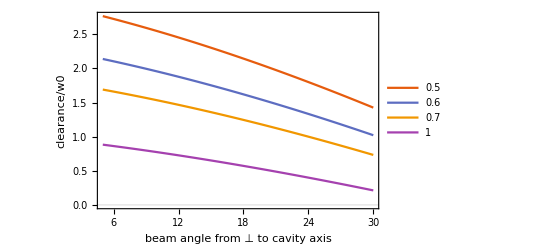

```mathematica
Clear[b,L,RoC,w0]
dm=0.022;(*mirror depth. calculate in elliptical_lens.nb*)
RoC=2;
rm=1;(*mechanical radius of mirror*)
L=2RoC-2dm;
b=rm Tan[θ]+w0/Cos[θ];
dc=(L/2-b)Cos[θ];
motBeamw0={0.5,0.6,0.7,1};
Plot[Evaluate[Table[dc/w0,{w0,motBeamw0}]/.θ->Θ π/180],{Θ,5,30},PlotLegends->motBeamw0,PlotTheme->"Scientific",FrameLabel->{"beam angle from ⊥ to cavity axis","clearance/w0"}]
```

Now plot for different mirror substrate radii but fixed MOT beam waist.

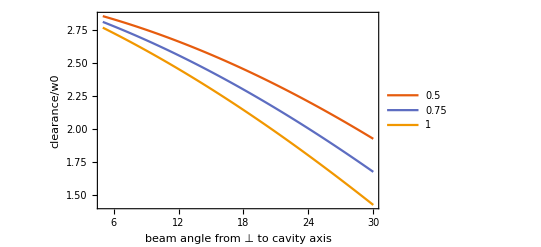

```mathematica
Clear[b,L,RoC,w0,rm]
dm=0.022;(*mirror depth. calculate in elliptical_lens.nb*)
RoC=2;
w0=0.5;
(*rm=0.75;*)(*mechanical radius of mirror*)
L=2RoC-2dm;
b=rm Tan[θ]+w0/Cos[θ];
dc=(L/2-b)Cos[θ];
rmvals={0.4,0.5,0.75,1};
Plot[Evaluate[Table[dc/w0,{rm,rmvals}]/.θ->Θ π/180],{Θ,5,30},PlotLegends->rmvals,PlotTheme->"Scientific",FrameLabel->{"beam angle from ⊥ to cavity axis","clearance/w0"}]
```